```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
(* Problem 1 Rotate an equilateral triangle RT=2 at the distance RR=7/2 from the origin. Rotate the triangle around itself.
The code highlighted by Cyan is attached to the Lab manual. 
*)
```

```mathematica
RT=2;
```

```mathematica
(* Shift the triangle along x *)
```

```mathematica
RR={7/2,0};
```

```mathematica
(* Center *)
```

```mathematica
CTri={0,0};
```

```mathematica
(* Shift the x coordinate by RR *)
```

```mathematica
Tri=RegularPolygon[CTri,RT,3]
```

RegularPolygon[{0,0},2,3]

```mathematica
(* Indicate the center by a point  *)
```

```mathematica
CTriP={Red,Point[CTri]}
```

{RGBColor[1, 0, 0],Point[{0,0}]}

```mathematica
(* The Triangle and the center point *)
```

```mathematica
ObjectTri={Tri,CTriP}
```

{RegularPolygon[{0,0},2,3],{RGBColor[1, 0, 0],Point[{0,0}]}}

```mathematica
(* ATTN: Compose the rotation function and apply to both the object and the centerpoint CTri. The composed transformation is generated by Composition  *)
```

```mathematica
TTri[a_]:=GeometricTransformation[ObjectTri,Composition[RotationTransform[a],TranslationTransform[RR]]]
```

```mathematica
(* Define the graphics function  *)
```

```mathematica
FTri[a_]:=Graphics[TTri[a],Axes->True, AxesOrigin->{0,0},PlotRange->5.5]
```

```mathematica
(* Check *)
```

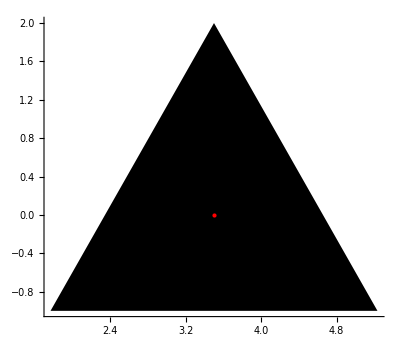
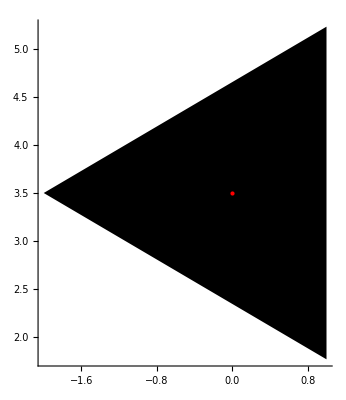
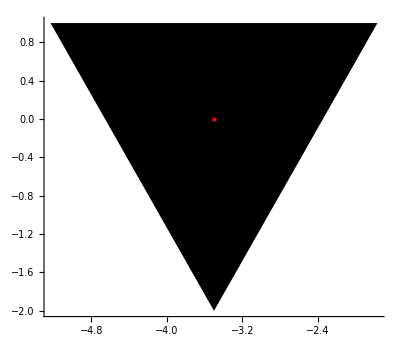

```mathematica
{FTri[0],FTri[Pi/2],FTri[Pi]}
```

```mathematica
FTriC[a_]:=Graphics[{Circle[CTri,RR[[1]]],TTri[a]},Axes->True,AxesOrigin->{0,0},PlotRange->5.5]
```

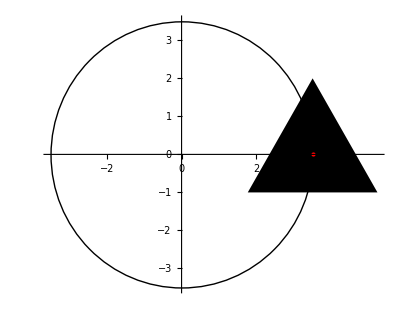
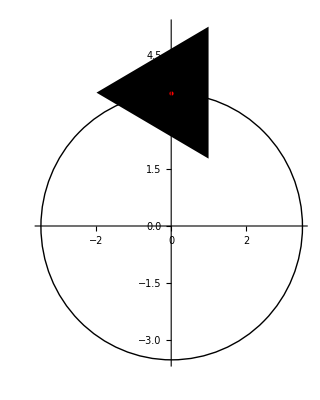
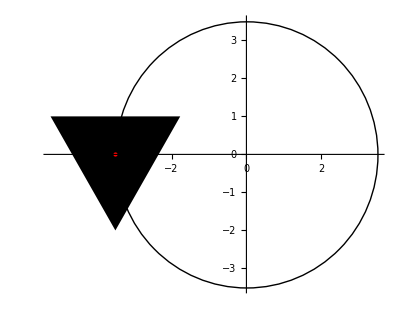

```mathematica
{FTriC[0],FTriC[Pi/2],FTriC[Pi]}
```

```mathematica
(* Animate triangle moving along the circular trajectory *)
```

```mathematica
Manipulate[FTriC[t],{t,0,2*Pi-0.01,0.1}]
```

```mathematica
TTriPlus[a_]:=GeometricTransformation[ObjectTri,Composition[RotationTransform[a],TranslationTransform[RR],RotationTransform[a]]]
```

```mathematica
FTriCPlus[a_] := Graphics[{{Magenta,Thickness[0.02],Circle[CTri,RR[[1]]]},TTriPlus[a]},Axes -> True, AxesOrigin -> {0,0}, PlotRange -> 5.5]
```

```mathematica
Manipulate[FTriCPlus[t],{t,0,2*Pi-0.01,0.1}]
```

```mathematica
(* Problem 2 *)
```

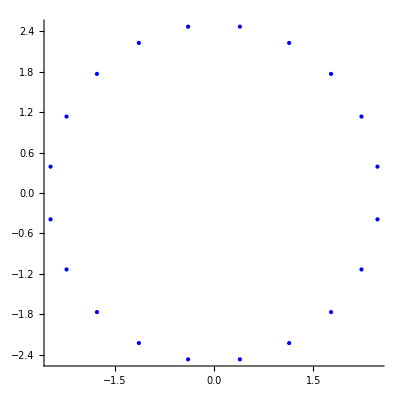

```mathematica
Graphics[{Blue, Point[CirclePoints[2.5,20]]},Axes->True]
```

```mathematica
Points := {Purple,PointSize -> 0.02,Point[CirclePoints[2,9]]}
```

```mathematica
ObjectTriPoints:={Points,ObjectTri}
```

```mathematica
TTriPoints[a_] := GeometricTransformation[ObjectTriPoints,Composition[RotationTransform[a],TranslationTransform[RR]]]
```

```mathematica
FPointsCir[a_] := Graphics[{TTriPoints[a]},Axes -> True, AxesOrigin -> {0,0}, PlotRange -> 5.5]
```

```mathematica
Manipulate[FPointsCir[t],{t,0,2*Pi-0.01,0.1}]
```

```mathematica
(* Problem 3 *)
```

```mathematica
NewCir2 := Circle[CTri,RT]
```

```mathematica
ObjectTriPoints1:={Points,ObjectTri,{Blue,NewCir2}}
```

```mathematica
TTriPointsCir[a_] := GeometricTransformation[ObjectTriPoints1,Composition[RotationTransform[a],TranslationTransform[RR],RotationTransform[5*a]]]
```

```mathematica
FPointsCircle[a_] := Graphics[{{Magenta,Thickness[0.015],Circle[CTri,RR[[1]]]},TTriPointsCir[a]},Axes -> True, AxesOrigin -> {0,0}, PlotRange -> 5.5]
```

```mathematica
Manipulate[FPointsCircle[t],{t,0,2Pi-0.01,0.1}]
```

```mathematica
(* Problem 4 *)
```

```mathematica
Traj[t_]:={t,0.05t^2}
```

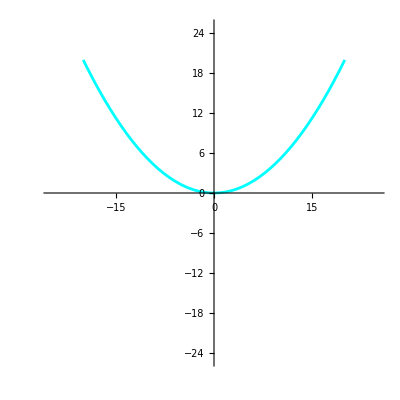

```mathematica
Tra = ParametricPlot[Traj[t],{t,-20,20},PlotRange->25,PlotStyle->Cyan]
```

```mathematica
(* Object *)
```

```mathematica
Ob[t_]:={4*Cos[2*t],4*Sin[4*t]}
```

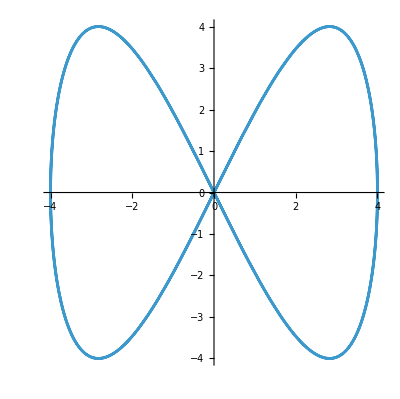

```mathematica
ParametricPlot[Ob[t],{t,0,2*Pi}]
```

```mathematica
(* Step 1 Translation *)
```

```mathematica
Tran=TranslationTransform[Traj[t]]
```

TransformationFunction[(1 | 0 | t
0 | 1 | 0.05 t^2
0 | 0 | 1)]

```mathematica
(* Step 2 Obtain the matrix of translation *)
```

```mathematica
MTran=TransformationMatrix[Tran]
```

{{1,0,t},{0,1,0.05 t^2},{0,0,1}}

```mathematica
(* Step 3 Convert the formula into matrix-function *)
```

```mathematica
FTran[t_]=Evaluate[MTran]
```

{{1,0,t},{0,1,0.05 t^2},{0,0,1}}

```mathematica
(* Step 4 Check *)
```

```mathematica
MatrixForm[FTran[t]]
```

(1 | 0 | t
0 | 1 | 0.05 t^2
0 | 0 | 1)

```mathematica
(* Apply the same procedure to derive the rotation matrix *)
```

```mathematica
Rot=RotationTransform[a]
```

TransformationFunction[(Cos[a] | -Sin[a] | 0
Sin[a] | Cos[a] | 0
0 | 0 | 1)]

```mathematica
MRot=TransformationMatrix[Rot]
```

{{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}}

```mathematica
FRot[a_]=Evaluate[MRot]
```

{{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}}

```mathematica
MatrixForm[FRot[a]]
```

(Cos[a] | -Sin[a] | 0
Sin[a] | Cos[a] | 0
0 | 0 | 1)

```mathematica
(* Combine the two transformations *)
```

```mathematica
MAll[a_,t_]=FTran[t].FRot[a]
```

{{Cos[a],-Sin[a],t},{0.+Sin[a],0.+Cos[a],0.05 t^2},{0,0,1}}

```mathematica
MatrixForm[MAll[a,t]]
```

(Cos[a] | -Sin[a] | t
0.+Sin[a] | 0.+Cos[a] | 0.05 t^2
0 | 0 | 1)

```mathematica
(* The object in the H cordinates *)
```

```mathematica
ObH[t_]:={4*Cos[2*t],4*Sin[4*t],1}
```

```mathematica
(* Apply MAll[a,t] to ObH[s] and cut off the H- coordinate *)
```

```mathematica
Res[a_,t_,s_]:=(MAll[a,t].ObH[s])[[1;;2]]
```

```mathematica
MatrixForm[Res[a,t,s]]
```

(t+4 Cos[a] Cos[2 s]-4 Sin[a] Sin[4 s]
0.05 t^2+4 Cos[2 s] (0.+Sin[a])+4 (0.+Cos[a]) Sin[4 s])

```mathematica
pres[a_,t_]:=ParametricPlot[Res[a,t,s],{s,0,2*Pi},PlotRange->6,PlotStyle->Magenta]
```

```mathematica
Manipulate[Show[Tra,pres[8*a,t]],{a,0,2*Pi},{t,-20,20}]
```

```mathematica
(* To simplify let us consider t function *)
```

```mathematica
T[a_]:=-20+((20*a)/Pi)
```

```mathematica
Manipulate[{Show[Tra,pres[a,T[a]]],"a=",a,"T[a]=",T[a]},{a,0,2*Pi}]
```

```mathematica
(* Using the rotation matrix rotate the entire system around the origin by the angle b. Animate. Synchronize a = b *)
```

```mathematica
MNew[a_,t_]= FRot[a].FTran[t].FRot[a]
```

{{Cos[a]^2-Sin[a]^2,-2 Cos[a] Sin[a],t Cos[a]-0.05 t^2 Sin[a]},{2 Cos[a] Sin[a],Cos[a]^2-Sin[a]^2,0.05 t^2 Cos[a]+t Sin[a]},{0.,0.,1.}}

```mathematica
ResNew[a_,t_,s_] := (MNew[a,t].ObH[s])[[1;;2]]
```

```mathematica
presNew[a_,t_] := ParametricPlot[ResNew[a,t,s],{s,-0,2Pi},PlotRange -> 6,PlotStyle -> Magenta]
```

```mathematica
TrajH[s_]:=  {s,0.05 s^2,1}
```

```mathematica
TrajNew[a_,s_] := (FRot[a].TrajH[s])[[1;;2]]
```

```mathematica
presTraj[a_] :=  ParametricPlot[TrajNew[a,s],{s,-20,20},PlotRange -> 25,PlotStyle -> Cyan]
```

```mathematica
Manipulate[Show[presTraj[a],presNew[a,T[a]]],{a,0,2Pi}]
```